```mathematica
dataset = Import["/Users/vincentleonardo/Documents/SUTD/2021/2021 Term 5/40.012 Manufacturing and Service Operations/SGH/mso-sgh-queue-project/consult_duration_clean.csv","Dataset", "HeaderLines" ->  1]
FindDistribution[dataset[1;;,2],3,"TargetFunctions"-> "Continuous"]
```

Dataset[<>]

{MixtureDistribution[{0.861654,0.138346},{LogNormalDistribution[3.29136,0.366281],LogNormalDistribution[4.30682,0.429055]}],MixtureDistribution[{0.896135,0.103865},{LogNormalDistribution[3.31999,0.386133],CauchyDistribution[78.9019,16.4786]}],LogNormalDistribution[3.43184,0.513801]}

```mathematica
{MixtureDistribution[{0.8616537846235686,0.1383462153764315},{LogNormalDistribution[3.2913550897808297,0.3662812531418911],LogNormalDistribution[4.306820606066296,0.4290550755065612]}],MixtureDistribution[{0.8961347288424863,0.10386527115751379},{LogNormalDistribution[3.319985670869931,0.386133126731984],CauchyDistribution[78.90185206490115,16.4786113735998]}],LogNormalDistribution[3.4318409008041986,0.5138008415469955]}
```

{MixtureDistribution[{0.861654,0.138346},{LogNormalDistribution[3.29136,0.366281],LogNormalDistribution[4.30682,0.429055]}],MixtureDistribution[{0.896135,0.103865},{LogNormalDistribution[3.31999,0.386133],CauchyDistribution[78.9019,16.4786]}],LogNormalDistribution[3.43184,0.513801]}

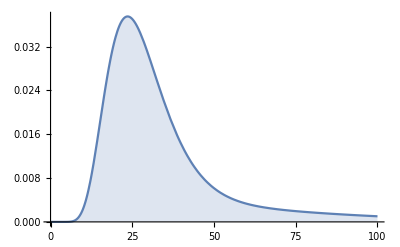

Show::gtype: Out is not a type of graphics.

```mathematica
𝒟=MixtureDistribution[{0.8616537846235686,0.1383462153764315},{LogNormalDistribution[3.2913550897808297,0.3662812531418911],LogNormalDistribution[4.306820606066296,0.4290550755065612]}];
Plot[PDF[𝒟,x],{x,0,100},Filling->Axis]
```